## Here we compute the cross section of p(p_1)+p̄(p_2)→J/ψ(p_ψ)+π(p_π)

```mathematica
(*Nucleon pole model for πN TDAs*)
```

```mathematica
(*Nucleon exchange model for πN TDAs *)
φ1piN[X1_,X2_,X3_,XI_,D2_]:=(gπNN*MN*fπ)/(D2-MN^2)*2*XI*1/(2*XI)^2*φN[X1/(2*XI),X2/(2*XI),X3/(2*XI)]
φ2piN[X1_,X2_,X3_,XI_,D2_]:=(gπNN*MN*fπ)/(D2-MN^2)*XI*1/(2*XI)^2*φN[X1/(2*XI),X2/(2*XI),X3/(2*XI)]

T4I12[X1_,X2_,X3_,XI_,D2_]:=0
T3I12[X1_,X2_,X3_,XI_,D2_]:=0

(*Here we express ``old'' Subscript[V, 1] Subscript[A, 1] and Subscript[T, 1] within the nucleon pole model for πN TDAs see App. A. of Pire et al. PRD 85*)

V1piN[X1_,X2_,X3_,XI_,D2_]:=(1-XI)/(1+XI)*1/2(φ1piN[X1,X2,X3,XI,D2]+φ1piN[X2,X1,X3,XI,D2])
A1piN[X1_,X2_,X3_,XI_,D2_]:=(1-XI)/(1+XI)*1/2(-φ1piN[X1,X2,X3,XI,D2]+φ1piN[X2,X1,X3,XI,D2])
T1piN[X1_,X2_,X3_,XI_,D2_]:=(1-XI)/(1+XI)*1/2(φ1piN[X1,X3,X2,XI,D2]+φ1piN[X2,X3,X1,XI,D2])

VN[a_,b_,c_]:=1/2(φN[a,b,c]+φN[b,a,c])
AN[a_,b_,c_]:=1/2(-φN[a,b,c]+φN[b,a,c])
TN[a_,b_,c_]:=1/2(φN[a,c,b]+φN[b,c,a])
```

```mathematica
Here we  express amplitudes in our model in terms of 2 Subscript[M, 0]
```

2 amplitudes express in^2 model of our terms we GeoPosition[{48.5,2.06}] M_0

```mathematica
DChernyak=Expand[(x1 (2 y1-1)-y1) (x3 (2 y3-1)-y3)];
DMy=Expand[(1-(2x1-1)(2y1-1))(1-(2x3-1)(2y3-1))];

Simplify[DChernyak/DMy]
```

1/4

Chernyak’s Z. Phys.’89 formula (23) defined it as  M_0= ∫(∫ (φ[x1,x2,x3]*φ[y1,y2,y3])/(x1 x2 x3 y1 y2 y3  (1-(2x1-1)(2y1-1))(1-(2x3-1)(2y3-1)))(y1x3)+(2T[x1,x2,x3]*T[y1,y2,y3])/(x1 x2 x3 y1 y2 y3  (1-(2x1-1)(2y1-1))(1-(2x2-1)(2y2-1)))*(y1x2)ⅆx)ⅆy 
(δ functions are implied)

```mathematica
Simplify[(2ξ)^2 Simplify[((ξ^3 (x1 y3+x3 y1)(V1piN[x1,x2,x3,ξ,Δ2]-A1piN[x1,x2,x3,ξ,Δ2])(φN[y1,y2,y3]))/(x1 x2 x3 y1 y2 y3 (m^2 (x1 (2 y1-1)-2 ξ y1)) (m^2 (x3 (2 y3-1)-2 ξ y3)))/.{x1->x1*2ξ,x2->x2*2ξ,x3->x3*2ξ})]/((φN[x1,x2,x3]*φN[y1,y2,y3])/(x1 x2 x3 y1 y2 y3  (1-(2x1-1)(2y1-1))(1-(2x3-1)(2y3-1)))*(x1 y3+x3 y1))]
Simplify[(2ξ)^2 Simplify[(2 ξ^3 (x1 y2+x2 y1)T1piN[x1,x2,x3,ξ,Δ2]TN[y1,y2,y3])/(x1 x2 x3 y1 y2 y3 (m^2 (x1 (2 y1-1)-2 ξ y1)) (m^2 (x2 (2 y2-1)-2 ξ y2)))/.{x1->x1*2ξ,x2->x2*2ξ,x3->x3*2ξ}]/((2TN[x1,x2,x3]*TN[y1,y2,y3])/(x1 x2 x3 y1 y2 y3  (1-(2x1-1)(2y1-1))(1-(2x2-1)(2y2-1)))(x1 y2+x2 y1))]
```

(fπ gπNN MN (-1+ξ))/(2 m^4 (MN^2-Δ2) (1+ξ))

(fπ gπNN MN (-1+ξ))/(2 m^4 (MN^2-Δ2) (1+ξ))

```mathematica
TeXForm[(fπ gπNN MN (-1+ξ))/(2 m^4 (MN^2-Δ2) (1+ξ)) ]
```

\frac{\text{f$\pi $} \text{g$\pi $NN} \text{MN} (\xi -1)}{2 m^4 (\xi +1) \left(\text{MN}^2-\text{$\Delta $2}\right)}

```mathematica
Here we  compute J/ψ->p p̄  decay width from the PDG data
```

(compute J we GeoPosition[{48.5,2.06}])/ψ→data decay from p PDG the width p̄

```mathematica
ΓppUp=(92.9+2.8)*(2.17+0.07)*(10^(-3));
ΓppDw=(92.9-2.8)*(2.17-0.07)*(10^(-3));
Print["Γ_(J/ψ → p OverscriptBox[p, _])= ",ΓppDw," ÷ ",ΓppUp," KeV" ]
```

Γ_(J/ψ → p OverscriptBox[p, _])= 0.18921 ÷ 0.214368 KeV

```mathematica
ΓJpsitoppMean=(0.18921000000000004+0.214368)/2
```

0.201789

```mathematica
M0={{"CZ",(120^2)*0.5248652162161354},{"KS",(120^2)*0.7991434173211521},{"COZ",(120^2)*0.6095056802540313},{"GS",(120^2)*0.08763041010225746},{"Asymp",6069.115650313606/4},{"BLW NLO",7209.4951068161/4},{"BLW NNLO",16676.274470743458/4},{"Bolz Krol",6594.827959256838/4},{"Stefanis heterotic",13756.97191680044}}
```

{{CZ,7558.06},{KS,11507.7},{COZ,8776.88},{GS,1261.88},{Asymp,1517.28},{BLW NLO,1802.37},{BLW NNLO,4169.07},{Bolz Krol,1648.71},{Stefanis heterotic,13757.}}

```mathematica
Here we  compute  Subscript[f, ψ] constant
```

compute constant we GeoPosition[{48.5,2.06}] f_ψ

```mathematica
ec=2/3;
αem=1/137;
Mpsi=3096;
Γeemax=(0.092+0.0028)*(0.0594+0.0006);
Γeemin=(0.092-0.0028)*(0.0594-0.0006);
fpsi:=fpsi
 
fmax=Solve[Γeemax==(4π*αem)^2*ec^2/(12*π)*fpsi^2/Mpsi,fpsi];
fmin=Solve[Γeemin==(4π*αem)^2*ec^2/(12*π)*fpsi^2/Mpsi,fpsi];

Print["f_ψ= ",(fpsi/.fmin[[2]])," ÷ " ,(fpsi/.fmax[[2]])," MeV"]
```

f_ψ= 404.612 ÷ 421.355 MeV

```mathematica
(421.35465033143174+404.61230636723343)/2
```

412.983

```mathematica
Here we  compute J/ψ->p p̄  decay width for different DA models
```

(compute J we GeoPosition[{48.5,2.06}])/ψ→DA decay different for models p width p̄

```mathematica
Alphas={}
fpsi=0.413
Print["f_ψ= ",fpsi," GeV"]
Mbar=3
For[i=1,i≤Length[M0],i++,{
αs=0.3,
If[M0[[i]][[1]]=="Bolz Krol",  fN:=6.64*10^(-3),fN:=5.0*10^(-3)],
Print["f_N= ",fN," GeV^2"],
Print["For α_s=0.3 ",M0[[i]][[1]]," DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = ",(π*αs)^6*1280/(243*π)*fpsi^2/Mbar*(fN/Mbar^2)^4*(M0[[i]][[2]])^2*10^3*10^3, " KeV"],
αs:=αs,
Sas=αs/.Solve[(π*αs)^6*1280/(243*π)*fpsi^2/Mbar*(fN/Mbar^2)^4*(M0[[i]][[2]])^2*10^3*10^3==ΓJpsitoppMean,αs][[6]],
Alphas=Append[Alphas,Sas],
Print["Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= ",Sas],
Print["______________________________________"]}]
```

{}

0.413

f_ψ= 0.413 GeV

3

f_N= 0.005 GeV^2

For α_s=0.3 CZ DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.363572 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.271961

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 KS DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.842838 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.2364

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 COZ DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.490286 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.258739

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 GS DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.0101345 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.493897

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 Asymp DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.0146521 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.464466

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 BLW NLO DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.0206756 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.438559

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 BLW NNLO DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.110624 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.331612

______________________________________

f_N= 0.00664 GeV^2

For α_s=0.3 Bolz Krol DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 0.0538082 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.373935

______________________________________

f_N= 0.005 GeV^2

For α_s=0.3 Stefanis heterotic DA gives Γ_(J/ψ → p OverscriptBox[p, _]) = 1.20452 KeV

Value of α_s for which Γ_(J/ψ → p OverscriptBox[p, _]) experimental is reproduced: α_s= 0.222742

______________________________________

```mathematica
Alphas
```

{0.271961,0.2364,0.258739,0.493897,0.464466,0.438559,0.331612,0.373935,0.222742}

```mathematica
Here we compute the cross section
```

compute cross section the we GeoPosition[{48.5,2.06}]

```mathematica
Solve[W2==((XI+1) Mbar^2)/(2 XI),XI]
```

{{XI→9/(-9+2 W2)}}

```mathematica
S[XI_]:=((XI+1) Mbar^2)/(2 XI)
N[Solve[((XI+1) Mbar^2)/(2 XI)==10,XI]]
N[Solve[((XI+1) Mbar^2)/(2 XI)==15,XI]]
N[Solve[((XI+1) Mbar^2)/(2 XI)==20,XI]]
```

{{XI→0.818182}}

{{XI→0.428571}}

{{XI→0.290323}}

```mathematica
Δ2max[XI_]:=(2 XI (MN^2 (-1+XI)+μ^2 (1+XI)))/(-1+XI^2)
Δ2max[0.8]
```

-4.44444 (-0.2 MN^2+1.8 μ^2)

```mathematica
Clear[MN,μ]
```

```mathematica
Clear[MN,μ]
```

```mathematica
Solve[Δt2==((1-XI) (DELTA2-2 XI (MN^2/(1+XI)-μ^2/(1-XI))))/(1+XI),DELTA2]
```

{{DELTA2→(-2 MN^2 XI+2 MN^2 XI^2-Δt2-2 XI Δt2-XI^2 Δt2+2 XI μ^2+2 XI^2 μ^2)/((-1+XI) (1+XI))}}

```mathematica
U[XI_,Δt2_]:=(-2 MN^2 XI+2 MN^2 XI^2-Δt2-2 XI Δt2-XI^2 Δt2+2 XI μ^2+2 XI^2 μ^2)/((-1+XI) (1+XI))
```

```mathematica
Λ[X_,Y_,Z_]:=√(X^2+Y^2+Z^2-2*X*Y-2*X*Z-2*Y*Z)
CalC=(4π*αs)^3(fpsi(fN)^2)/fπ 10/81;
CC=CalC*((fπ gπNN MN (-1+ξ))/(2 (MN^2-Δ2) (1+ξ)));
```

```mathematica
MN=940/1000;
Print["M_N= ",N[MN]," Gev"]
μ=0;
Print["m_π= ",μ," Gev"]
gπNN:=1321/100
fπ:=93/1000
(*M̄=3 GeV see CZ Z.Phys'89 M̄=2m*)
 Mbar=3;
Print["M̄= ", Mbar," Gev"]
 fN:=5.0*10^(-3);
Print["f_N= ",fN," GeV^2"]
(*see CZ Z.Phys'89 M̄=2m*)
fpsi=0.383;
Print["f_ψ= ",fpsi," GeV^2"]
αs=0.2520617559544493;
Print["α_s= ",αs]
```

M_N= 0.94 Gev

m_π= 0 Gev

M̄= 3 Gev

f_N= 0.005 GeV^2

f_ψ= 0.383 GeV^2

α_s= 0.252062

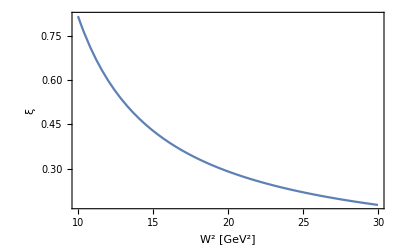

```mathematica
Plot[-Mbar^2/(Mbar^2-2 W2),{W2,10,30},Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"W^2 [GeV^2]","ξ",""},PlotRange->All,Axes->None]
```

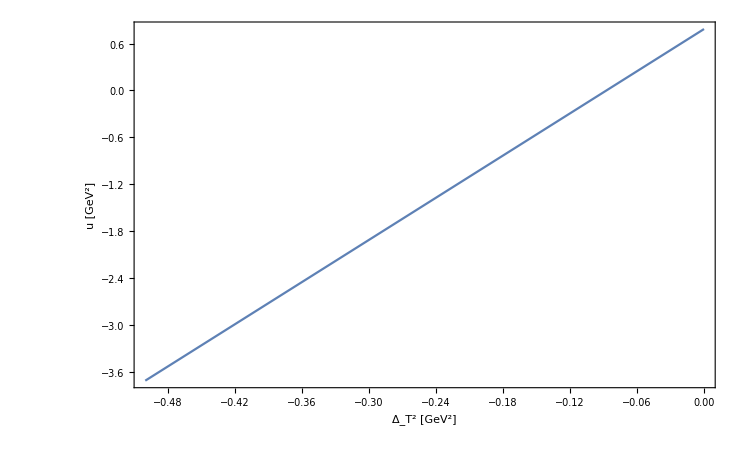

```mathematica
Plot[U[0.8,Δt2],{Δt2,0,-0.5},Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Δ_T^2  [GeV^2]","u  [GeV^2]","ξ=0.8 ",""},PlotRange->All,Axes->None]
```

```mathematica
CSDu[XI_,U_,NN_]:=((0.3894*10^-3)*1/(64*π*s)1/((Λ[s,MN^2,MN^2]^2)/(4*s))*1/4(2*(1+ξ))/ξ 1/Mbar^8*(CC^2*(2*M0[[NN]][[2]])^2-(((1-ξ) (Δ2-2 ξ (MN^2/(1+ξ)-μ^2/(1-ξI))))/(1+ξ))/MN^2((1+ξ)/(1-ξ))^2 CC^2(2*M0[[NN]][[2]])^2))/.{s->((XI+1) Mbar^2)/(2 XI),ξ->XI,Δ2->U}
CSDomega[XI_,U_,NN_]:=((0.3894*10^-3)*2*π*1/(64*π^2*s)Λ[s,Mbar^2,mπ^2]/Λ[s,MN^2,MN^2]*1/4(2*(1+ξ))/ξ 1/Mbar^8*CC^2*(2*M0[[NN]][[2]])^2)/.{s->((XI+1) Mbar^2)/(2 XI),ξ->XI,Δ2->U}

(*CSDu[XI_,U_,NN_]:=((0.3894*10^-3)*1/(16*π)1/(Λ[s,MN^2,MN^2]^2)*1/4(2*(1+ξ))/ξ 1/Mbar^8*CC^2*(2*M0[[NN]][[2]])^2)/.{s->((XI+1) Mbar^2)/(2 XI),ξ->XI,Δ2->U}*)
```

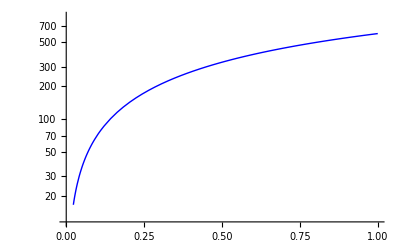

```mathematica
CSuCOZ=LogPlot[CSDu[XI,U[XI,0],3]/10^(-12),{XI,0,0.999},PlotStyle->{Blue,Thick}]
```

```mathematica
DELTAT[Θ_,W_]:=(4 ((W+√(W^2-4MN^2))/(4(1+ξ)))^2 (ξ-1)^2 (Cos[Θ]+1))/(Cos[Θ]-1)/.{ξ->-Mbar^2/(Mbar^2-2 W^2)}
DELTAT1[Θ_,W_]:=(4 ((W+√(W^2-4MN^2))/(4(1+ξ)))^2 (ξ-1)^2 (Cos[Θ]-1))/(Cos[Θ]+1)/.{ξ->-Mbar^2/(Mbar^2-2 W^2)}
```

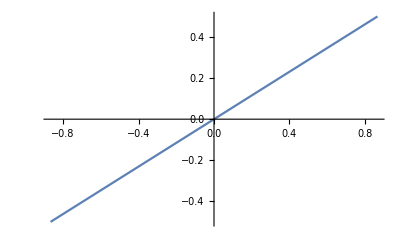

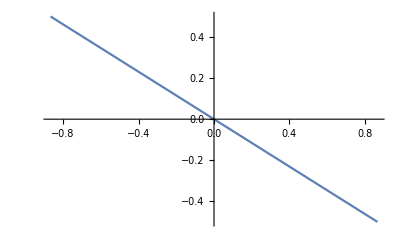

```mathematica
gg0=Plot[Tan[π/6]x,{x,-(√3)/2,(√3)/2}]
gg=Plot[-Tan[π/6]x,{x,-(√3)/2,(√3)/2}]
```

```mathematica
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]]/.{W->√10})==-1,Θ]
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]]/.{W->√15})==-1,Θ]
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]]/.{W->√20})==-1,Θ]
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]]/.{W->√25})==-1,Θ]
```

{{Θ→ConditionalExpression[1. (-1.95652+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (1.95652+6.28319 C[1]),C[1]∈Integers]}}

{{Θ→ConditionalExpression[1. (-0.988522+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (0.988522+6.28319 C[1]),C[1]∈Integers]}}

{{Θ→ConditionalExpression[1. (-0.715375+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (0.715375+6.28319 C[1]),C[1]∈Integers]}}

{{Θ→ConditionalExpression[1. (-0.579155+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (0.579155+6.28319 C[1]),C[1]∈Integers]}}

```mathematica
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√10})==-1,Θ]
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√15})==-1,Θ]
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√20})==-1,Θ]
NSolve[(U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√25})==-1,Θ]
```

{{Θ→ConditionalExpression[1. (-1.18507+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (1.18507+6.28319 C[1]),C[1]∈Integers]}}

{{Θ→ConditionalExpression[1. (-2.15307+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (2.15307+6.28319 C[1]),C[1]∈Integers]}}

{{Θ→ConditionalExpression[1. (-2.42622+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (2.42622+6.28319 C[1]),C[1]∈Integers]}}

{{Θ→ConditionalExpression[1. (-2.56244+6.28319 C[1]),C[1]∈Integers]},{Θ→ConditionalExpression[1. (2.56244+6.28319 C[1]),C[1]∈Integers]}}

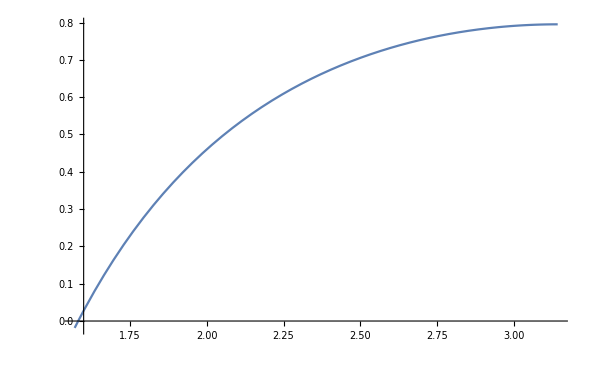

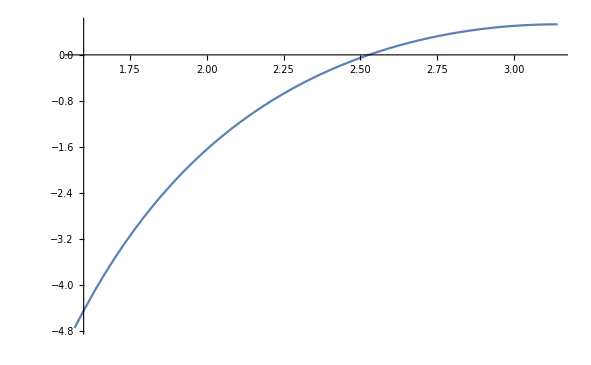

-Graphics-

```mathematica
Plot[U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√10},{Θ,π, π/2},PlotRange->All]
Plot[U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√15},{Θ,π, π/2},PlotRange->All]
Plot[U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]]/.{W->√15},{Θ,π, π/2},PlotRange->All]
```

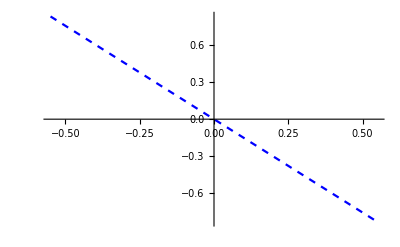

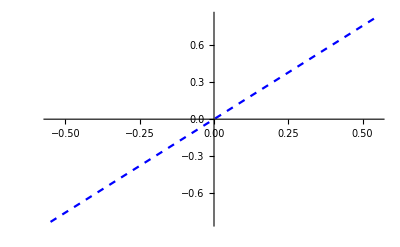

```mathematica
gg0=Plot[Tan[ 2.1530704127841944]x,{x,-Cos[2.1530704127841944],Cos[2.1530704127841944]},PlotStyle->{Blue,Dashed}]
gg00=Plot[-Tan[ 2.1530704127841944]x,{x,-Cos[2.1530704127841944],Cos[2.1530704127841944]},PlotStyle->{Blue,Dashed }]
```

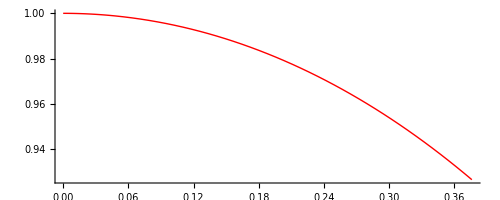

```mathematica
PolarPlot[ 1/.{W->√10},{Θ, 1.185072594212219,π/2},PlotStyle->{Red,Thick}]
```

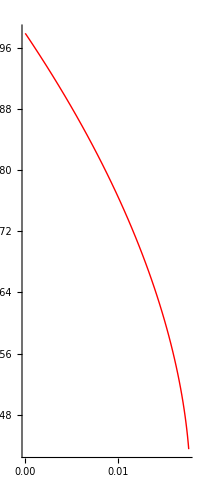

```mathematica
g1=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√10},{Θ, 1.185072594212219,π/2},PlotStyle->{Red,Thick}]
```

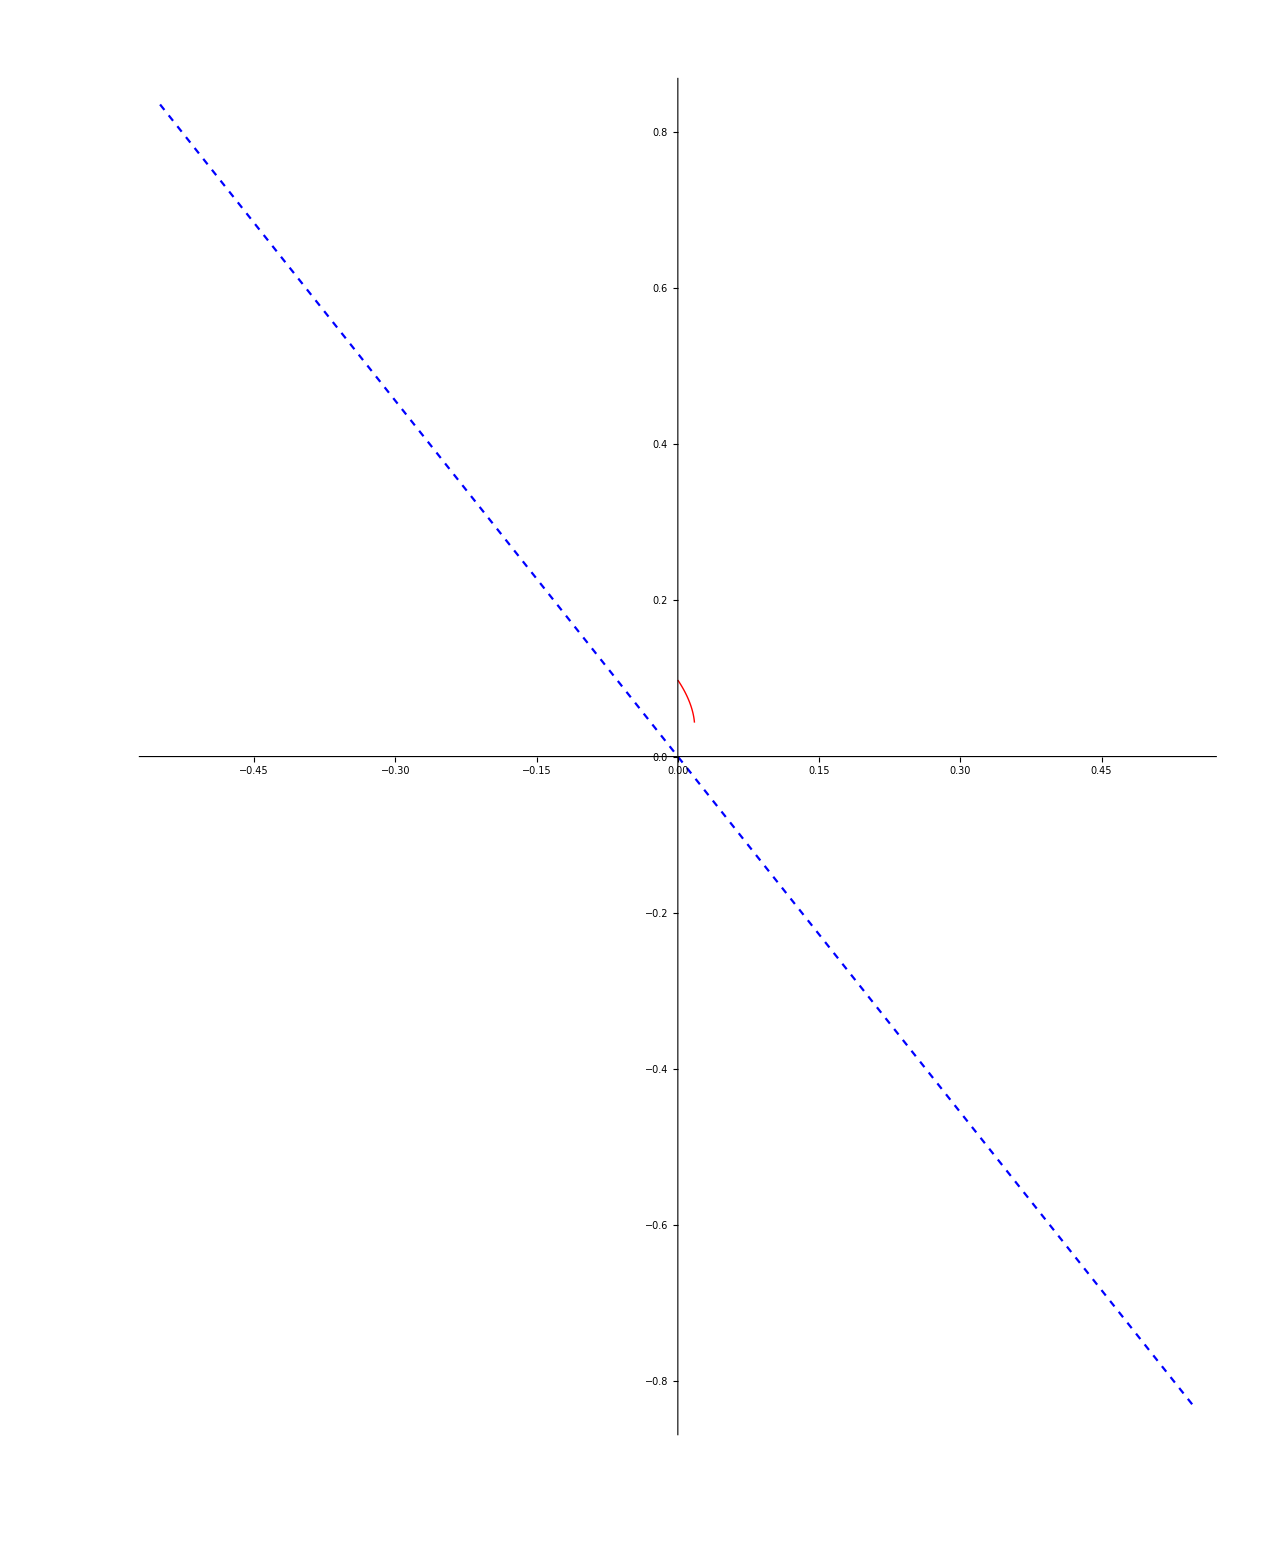

```mathematica
Show[g1,gg0]
```

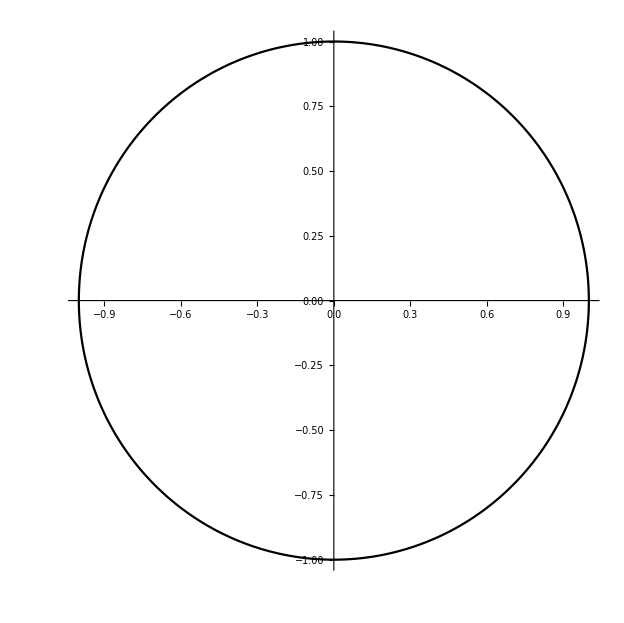

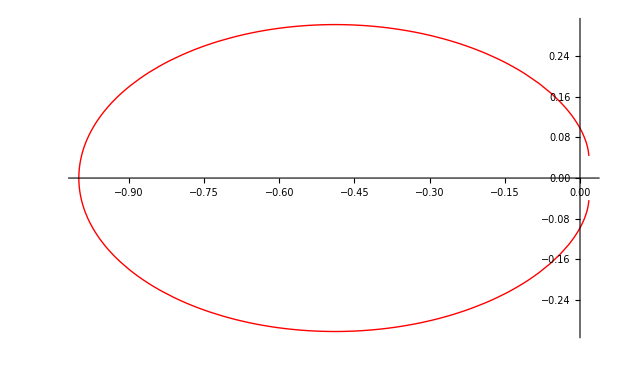

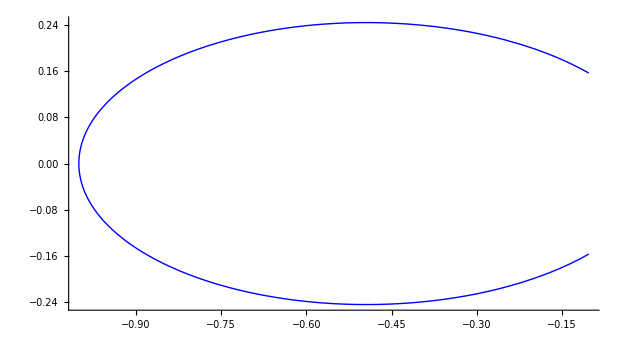

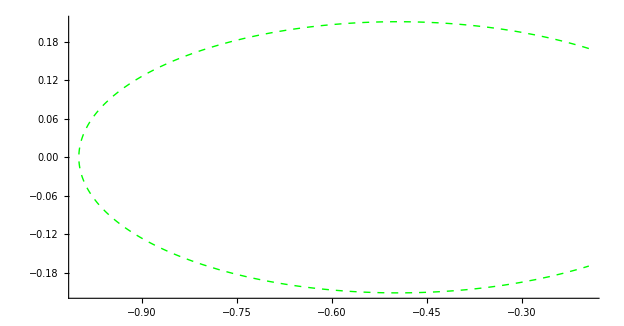

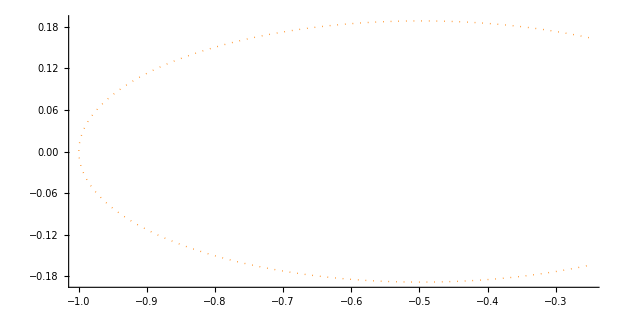

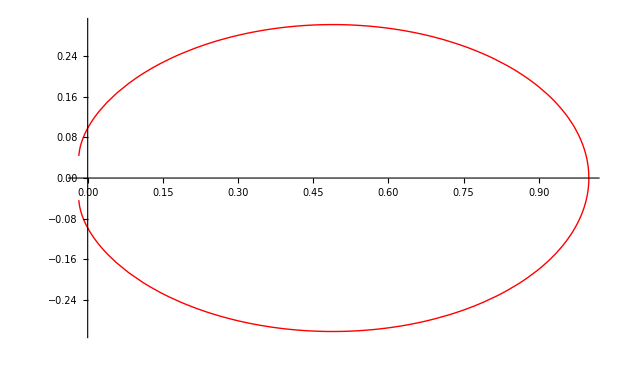

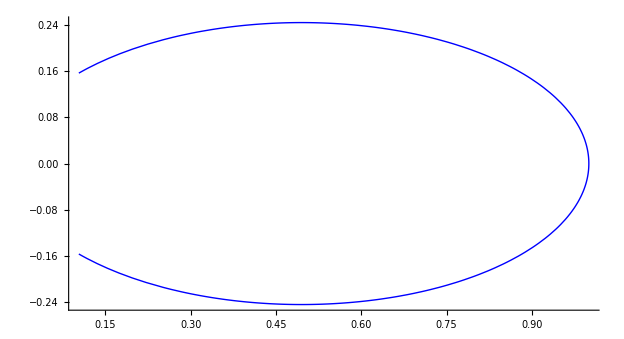

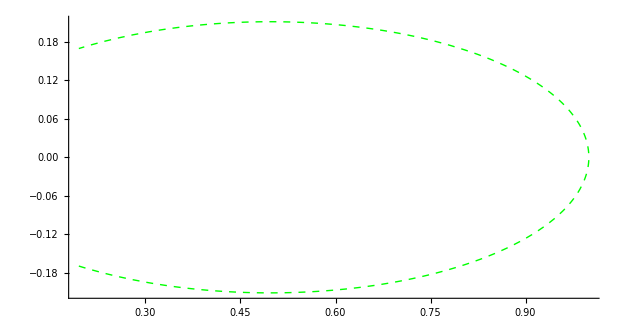

```mathematica
g0=PolarPlot[ 1/.{W->√10},{Θ,0,2π},PlotStyle->{Black }]
g1=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√10},{Θ, 1.185072594212219,2π- 1.185072594212219},PlotStyle->{Red,Thick}]
g2=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√15},{Θ,2.1530704127841944, 2π-2.1530704127841944},PlotStyle->{Blue,Thick}]

g3=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√20},{Θ,2.426218144500988,2π-2.426218144500988},PlotStyle->{Green,Dashed,Thick}]

g4=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√25},{Θ,2.562437425064001,2π-2.562437425064001},PlotStyle->{Orange,Dotted,Thick}]

g1t=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√10},{Θ,-1.9565200593775742, 1.9565200593775742},PlotStyle->{Red,Thick}]
g2t=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√15},{Θ, -0.9885222408055987,0.9885222408055987},PlotStyle->{Blue,Thick}]

g3t=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√20},{Θ, -0.715374509088805,0.715374509088805},PlotStyle->{Green,Dashed,Thick}]
g4t=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT1[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√25},{Θ, -0.5791552285257925,0.5791552285257925},PlotStyle->{Orange,Dotted,Thick}]

Show[gg0,gg00,g0,g4,g2,g3,g4t,g2t,g3t,PlotRange->All,Frame->True,FrameTicks->None]
```

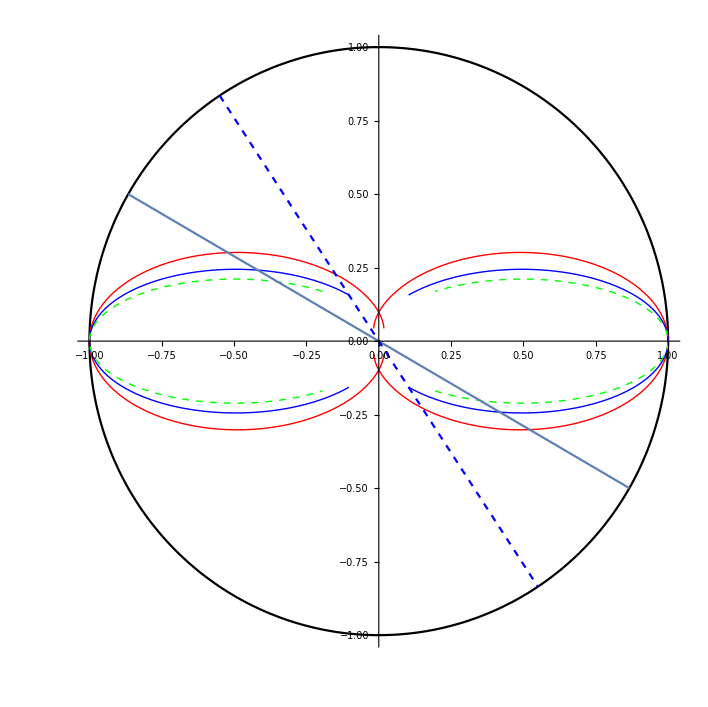

```mathematica
Show[g0,g1,g2,g3,g1t,g2t,g3t,gg,gg0,PlotRange->All]
```

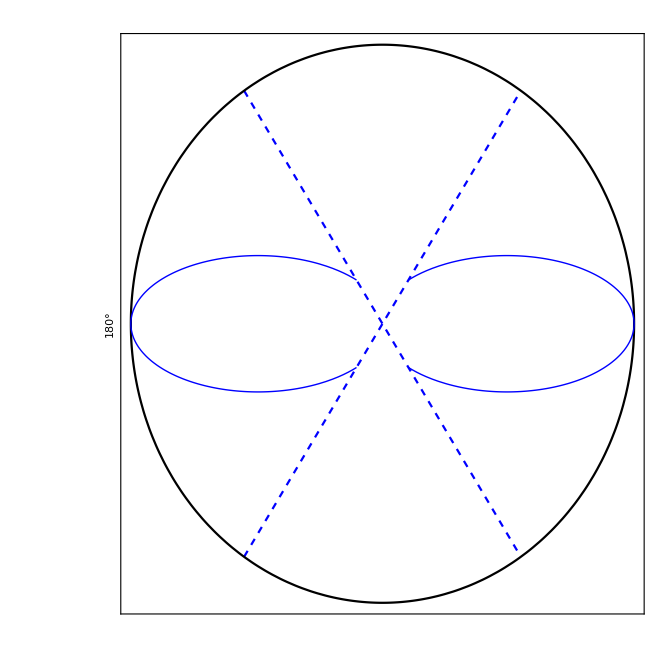

```mathematica
Show[gg0,gg00,g0, g2, g2t ,PlotRange->All,Frame->True,FrameTicks->None,AspectRatio->1,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"","180°","p̄p_→ J/ψ π^0;   W^2=15 GeV^2;","0°"},RotateLabel->False]
```

-Graphics-

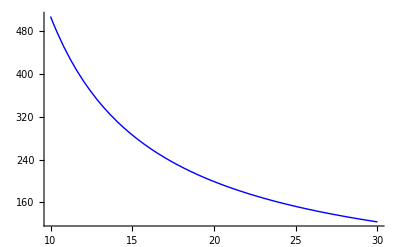

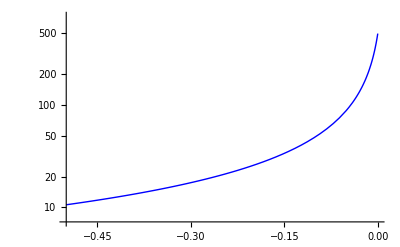

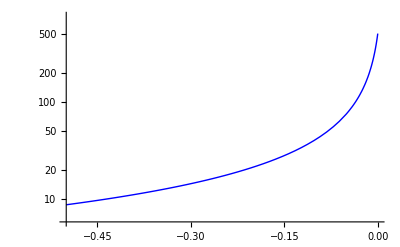

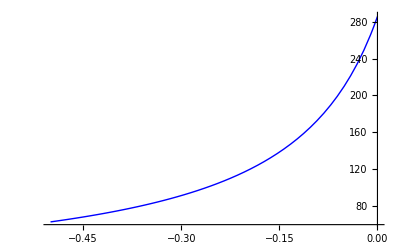

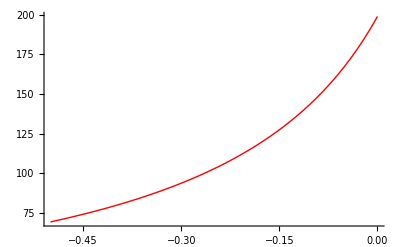

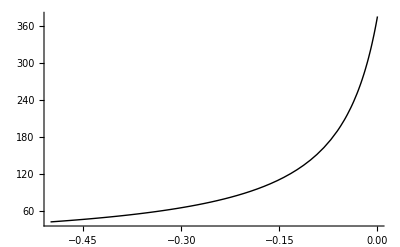

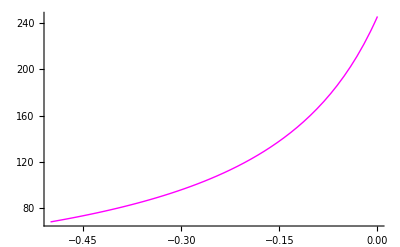

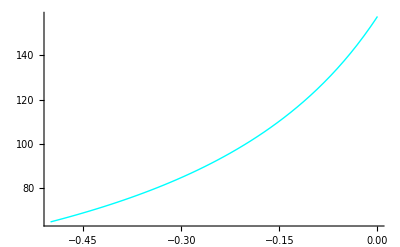

```mathematica
CSuCOZ=LogPlot[CSDu[XI,U[XI,0],3]/10^(-12),{XI,0,0.999},PlotStyle->{Blue,Thick}]
CSuCOZW2=Plot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),0],3]/10^(-12),{W2,10,30},PlotStyle->{Blue,Thick}]



CSuCOZΔt2=LogPlot[CSDu[0.8,U[0.8,Δt2],3]/10^(-12),{Δt2,0,-0.5},PlotStyle->{Blue,Thick}]

CSuCOZΔt21=LogPlot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->10,{Δt2,0,-0.5},PlotStyle->{Blue,Thick}]
CSuCOZΔt22=Plot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->15,{Δt2,0,-0.5},PlotStyle->{Blue,Thick}]

CSuCOZΔt23=Plot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->20,{Δt2,0,-0.5},PlotStyle->{Red,Thick}]

CSuCOZΔt24=Plot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->12.26,{Δt2,0,-0.5},PlotStyle->{Black,Thick}, PlotRange->All]

CSuCOZΔt25=Plot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->16.8745,{Δt2,0,-0.5},PlotStyle->{Magenta,Thick}]

CSuCOZΔt26=Plot[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->24.346,{Δt2,0,-0.5},PlotStyle->{Cyan,Thick}]
```

```mathematica
minval = -0.25225
maxval = -0.01
energy = 12.26
N[-Mbar^2/(Mbar^2-2 energy)]
N[U[-Mbar^2/(Mbar^2-2 W2),minval]/. W2 -> energy]
N[U[-Mbar^2/(Mbar^2-2 W2),maxval]/. W2 -> energy]
N[Integrate[CSDu[-Mbar^2/(Mbar^2-2 W2),U[-Mbar^2/(Mbar^2-2 W2),Δt2],3]/10^(-12)/.W2->energy, {Δt2, minval, maxval}]]

N[Integrate[CSDu[0.579897,U[0.579897,Δt2],3]/10^(-12), {Δt2, minval, maxval}]]

N[Integrate[CSDu[0.579897,del,3]/10^(-12), {del, -0.3, 0.6}]]
```

-0.25225

-0.01

12.26

0.579897

-0.3

0.611039

34.4373

34.4373

126.008

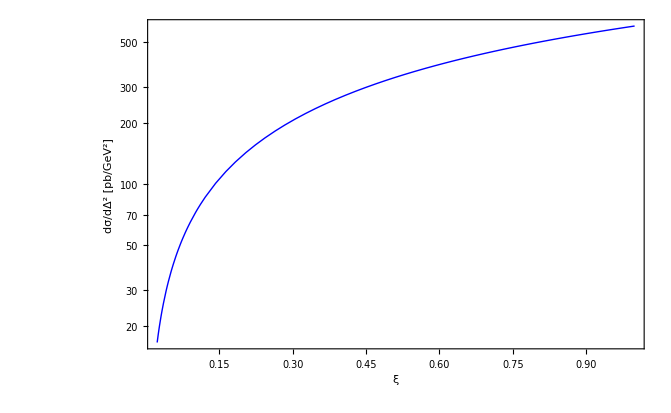

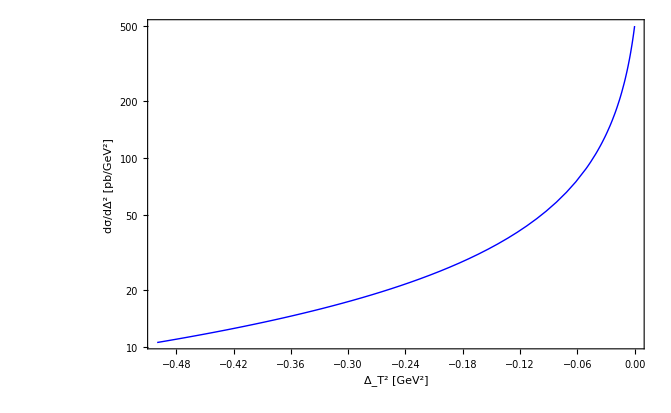

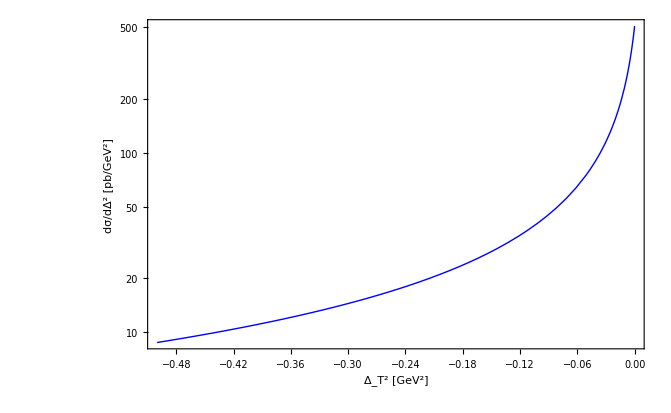

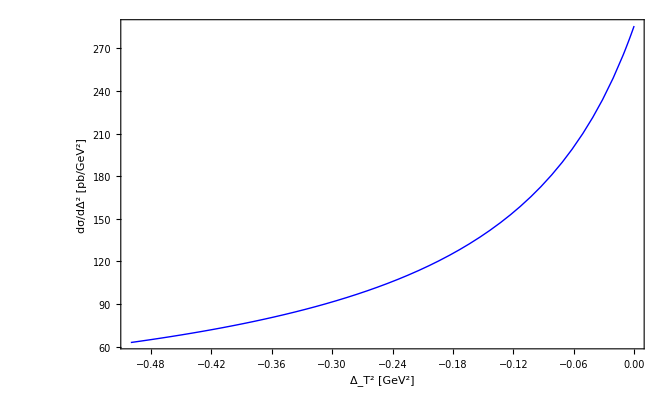

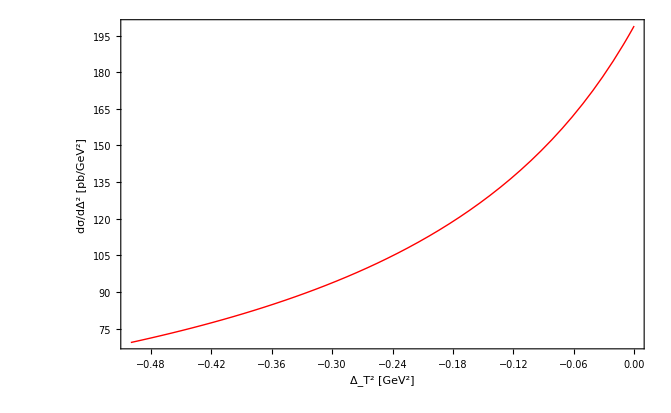

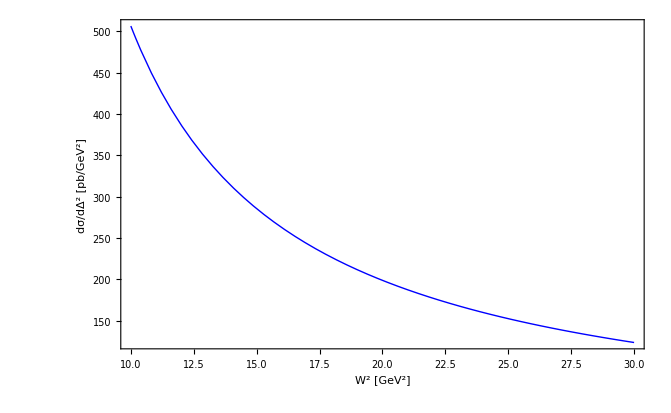

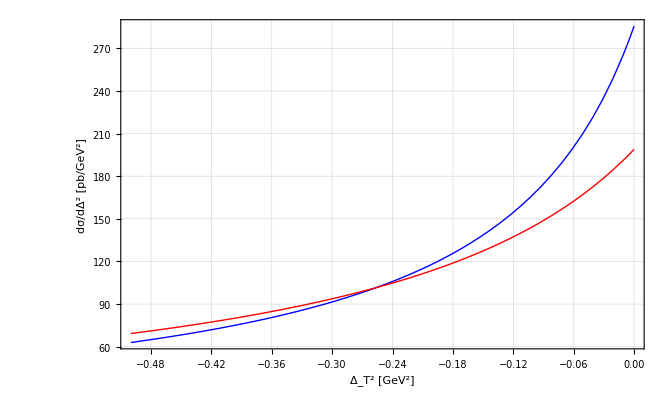

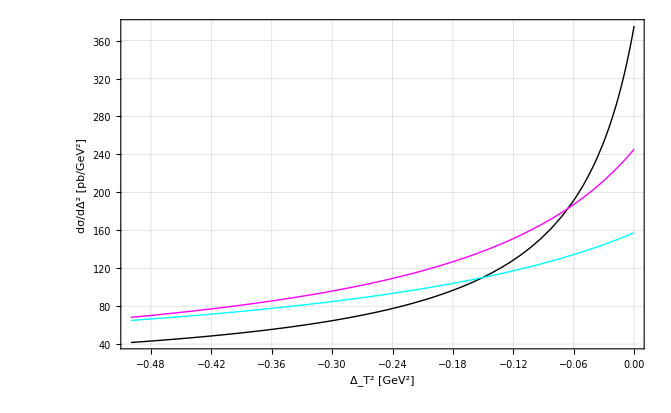

```mathematica
Show[CSuCOZ,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"ξ","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0; |Δ_T^2|= 0 GeV^2;",""},PlotRange->All,Axes->None]
Show[CSuCOZΔt2,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Δ_T^2  [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0;  ξ= 0.8 (W^2=10 GeV^2);",""},PlotRange->All,Axes->None]

Show[CSuCOZΔt21,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Δ_T^2  [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0; W^2=10 GeV^2;",""},PlotRange->All,Axes->None]

Show[CSuCOZΔt22,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Δ_T^2  [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0;  W^2=15 GeV^2;",""},PlotRange->All,Axes->None]

Show[CSuCOZΔt23,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Δ_T^2  [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0;  W^2=20 GeV^2;",""},PlotRange->All,Axes->None]

Show[CSuCOZW2,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"W^2 [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0;  |Δ_T^2|= 0 GeV^2;",""},PlotRange->All,Axes->None]

Show[{CSuCOZΔt22, CSuCOZΔt23}, Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Δ_T^2  [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0;  W^2=15, 20 GeV^2;",""},PlotRange->All,Axes->None, PlotRange->All, GridLines->Automatic]

Show[CSuCOZΔt24, CSuCOZΔt25, CSuCOZΔt26, Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],
FrameLabel->{"Δ_T^2  [GeV^2]","dσ/dΔ^2 [pb/GeV^2]","p̄p_→ J/ψ π^0;  W^2=12.26, 16.87, 24.35 GeV^2;",""},PlotRange->All,Axes->None, PlotRange->All, GridLines->Automatic]
```

```mathematica
NSolve[10==(x+√(9+x^2))^2,x]
```

{{x→0.158114}}

```mathematica
N[(1/(2 √10))^2]
```

0.025

```mathematica
Solve[15==(x+√(9+x^2))^2,x]
```

{{x→√(3/5)}}

```mathematica
N[√(3/5)]
```

0.774597

```mathematica
0.7745966692414834^2
```

0.6

```mathematica
(√3)/4.^2
```

0.1875

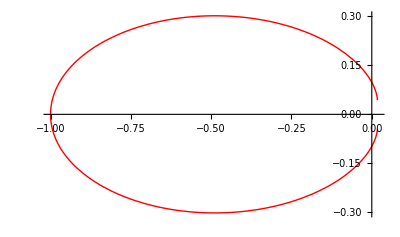

```mathematica
g1=PolarPlot[ CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]/CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),0],3]/.{W->√10},{Θ, 1.185072594212219,2π- 1.185072594212219},PlotStyle->{Red,Thick}]
```

```mathematica
CSDu[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]
```

1/(-(2209 (-9+2 W^2) (1-9/(9-2 W^2)))/1250+1/4 (-9+2 W^2)^2 (1-9/(9-2 W^2))^2)6.55969×10^-11 (-9+2 W^2) (1-9/(9-2 W^2)) ((19.4918 (-1-9/(9-2 W^2))^2)/((1-9/(9-2 W^2))^2 (2209/2500-(178929/(1250 (9-2 W^2)^2)+19881/(1250 (9-2 W^2))-((-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(4 (1-9/(9-2 W^2))^2 (-1+Cos[Θ]))-(81 (-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(4 (9-2 W^2)^2 (1-9/(9-2 W^2))^2 (-1+Cos[Θ]))+(9 (-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(2 (9-2 W^2) (1-9/(9-2 W^2))^2 (-1+Cos[Θ])))/((-1-9/(9-2 W^2)) (1-9/(9-2 W^2))))^2)-(22.0596 (-1-9/(9-2 W^2))^2 (19881/(1250 (9-2 W^2) (1-9/(9-2 W^2)))+(178929/(1250 (9-2 W^2)^2)+19881/(1250 (9-2 W^2))-((-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(4 (1-9/(9-2 W^2))^2 (-1+Cos[Θ]))-(81 (-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(4 (9-2 W^2)^2 (1-9/(9-2 W^2))^2 (-1+Cos[Θ]))+(9 (-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(2 (9-2 W^2) (1-9/(9-2 W^2))^2 (-1+Cos[Θ])))/((-1-9/(9-2 W^2)) (1-9/(9-2 W^2)))))/((1-9/(9-2 W^2)) (1+9/(9-2 W^2)) (2209/2500-(178929/(1250 (9-2 W^2)^2)+19881/(1250 (9-2 W^2))-((-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(4 (1-9/(9-2 W^2))^2 (-1+Cos[Θ]))-(81 (-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(4 (9-2 W^2)^2 (1-9/(9-2 W^2))^2 (-1+Cos[Θ]))+(9 (-1-9/(9-2 W^2))^2 (W+√(-2209/625+W^2))^2 (1+Cos[Θ]))/(2 (9-2 W^2) (1-9/(9-2 W^2))^2 (-1+Cos[Θ])))/((-1-9/(9-2 W^2)) (1-9/(9-2 W^2))))^2))

```mathematica
W=√25
```

5

```mathematica
mπ=0
```

0

```mathematica
N[W]
```

5.

```mathematica
NIntegrate[CSDomega[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3],{Θ,0,2π}]/10^(-9)
```

0.675006

```mathematica
-Mbar^2/(Mbar^2-2 W^2)
```

9/41

```mathematica
CSDomega[-Mbar^2/(Mbar^2-2 W^2),U[-Mbar^2/(Mbar^2-2 W^2),DELTAT[Θ,W]],3]
```

(3.61722×10^-10)/((2209/2500+(1681 (-318096/1050625-(256 (5+(2 √3354)/25)^2 (1+Cos[Θ]))/(1681 (-1+Cos[Θ]))))/1600)^2)